```mathematica
ClearAll["Global`*"]
```

```mathematica
t[x_,y_,x0_,y0_,a_,b_,c_,d_]=({{a, b}, {c, d}}).({{x-x0}, {y-y0}})
f[{x_,y_}]=FullSimplify[(2 BesselJ[1,√(x^2+y^2)]/(√(x^2+y^2)))^2,x^2+y^2>0]
fp[x_,y_,x0_,y0_,z0_,sz_,a_,b_,c_,d_]=sz*f[t[x,y,x0,y0,a,b,c,d]]+z0
fm[x_,y_,x0_,y0_,z0_,sz_,a_,b_,c_,d_]=Min[fp[x,y,x0,y0,z0,sz,a,b,c,d],255]
```

{{a (x-x0)+b (y-y0)},{c (x-x0)+d (y-y0)}}

Hypergeometric0F1Regularized[2,1/4 (-x^2-y^2)]^2

{z0+sz Hypergeometric0F1Regularized[2,1/4 (-(a (x-x0)+b (y-y0))^2-(c (x-x0)+d (y-y0))^2)]^2}

Min[255,z0+sz Hypergeometric0F1Regularized[2,1/4 (-(a (x-x0)+b (y-y0))^2-(c (x-x0)+d (y-y0))^2)]^2]

```mathematica
Manipulate[DensityPlot[fp[x,y,x0,y0,z0,sz,a,b,c,d],{x,0,255},{y,0,255},PlotRange->{0,255},PlotPoints->40],{{a,1},-2,2},{{b,0},-2,2},{{c,0},-2,2},{{d,1},-2,2},{{x0,63},0,127},{{y0,63},0,127},{{z0,0},-255,255},{{sz,4095},-8191,8191}]
```

```mathematica
laserdata=Import["C:\\Users\\Benjamin\\OneDrive\\Documents\\UQAR\\2017 Été\\Stage I\\mathematica-test\\laser3.bmp", "RawData"];
side=Length[laserdata];
size=side*side;
lasermatrix=Table[0,size,3];
lasermatrix⟦All,1⟧=Table[Quotient[i,side],{i,0,size-1}];
lasermatrix⟦All,2⟧=Table[Mod[i,side],{i,0,size-1}];
lasermatrix⟦All,3⟧=Flatten[laserdata];
```

```mathematica
fittedDiffraction=NonlinearModelFit[lasermatrix,{fm[x,y,x0,y0,z0,sz,a,b,c,d]},{{x0,side/2},{y0,side/2} ,{z0,8},{sz,8192},{a,0.5},{b,0},{c,0},{d,0.5}},{x,y}]
```

NonlinearModelFit::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

FittedModel[Min[255,8.53359+52102.1 Hypergeometric0F1Regularized[2,1/4 (-(«1»)^2-(-«20» (-«18»+x)+«1»)^2)]^2]]

```mathematica
fx0=x0/.fittedDiffraction["BestFitParameters"]
fy0=y0/.fittedDiffraction["BestFitParameters"]
fz0=z0/.fittedDiffraction["BestFitParameters"]
fsz=sz/.fittedDiffraction["BestFitParameters"]
fa=a/.fittedDiffraction["BestFitParameters"]
fb=b/.fittedDiffraction["BestFitParameters"]
fc=c/.fittedDiffraction["BestFitParameters"]
fd=d/.fittedDiffraction["BestFitParameters"]
Show[{
ListDensityPlot[
lasermatrix,
PlotRange->{0,255},
ColorFunction->"CherryTones",
Epilog->{
Green,Point[{fx0,fy0}]}],
DensityPlot[
fp[x,y,fx0,fy0,fz0,fsz,fa,fb,fc,fb],
{x,0,127},
{y,0,127},
PlotRange->{0,255},
PlotPoints->100,
PlotStyle->Opacity[0.3]]}]
```

63.2863

64.1267

8.53359

52102.1

1.40793

-0.012094

-0.078373

1.5345

-Graphics-

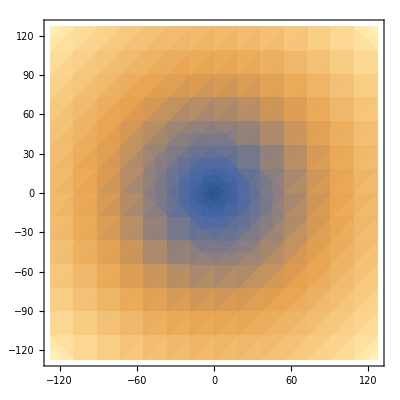

```mathematica
DensityPlot[√(x^2+y^2),{x,-127,127},{y,-127,127}]
```